(8. | 0 | 1. | 0.7173 | 0.1248
8. | 1 | 0.5 | 0.7959 | 0.1513
8. | 2 | 0.3333 | 0.8591 | 0.1726
8. | 3 | 0.25 | 0.8864 | 0.1831
8. | 4 | 0.2 | 0.908 | 0.1912
8. | 5 | 0.1667 | 0.9215 | 0.1965
8. | 6 | 0.1429 | 0.9324 | 0.2007
8. | 7 | 0.125 | 0.9404 | 0.2039
8. | 8 | 0.1111 | 0.947 | 0.2064
8. | 9 | 0.1 | 0.9523 | 0.2085
8. | 10 | 0.0909 | 0.9567 | 0.2102
8. | 11 | 0.0833 | 0.9605 | 0.2117
8. | 12 | 0.0769 | 0.9637 | 0.2129
8. | 9999 | 0. | 1. | 0.25)

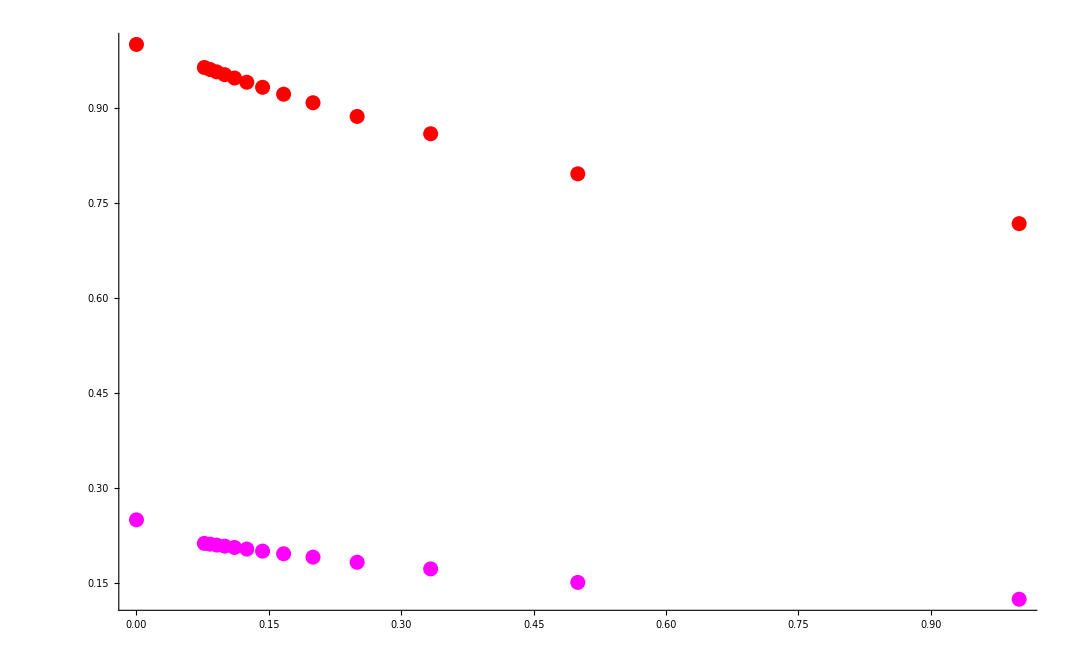

```mathematica
(* Useful functions for formatting *)
fsndig[x_,n_]:=ToString[PaddedForm[x,{n+2,n},NumberPadding->{"","0"}]];
(* Parameters *)
λ0=8.0;
s1s2s3="mp";
(* Data file name *)
F=Import["G:\\LAT\\sd_metropolis\\data\\smlm_analytics\\lu_s2_"<>s1s2s3<>"_l"<>fsndig[λ0,2]<>".dat"];
Print[MatrixForm[F]];
F=Transpose[F];
X=F[[3]];YU=F[[4]]; YL=F[[5]];
XYU=Transpose[{X, YU}];XYL=Transpose[{X, YL}];
ListPlot[{XYU,XYL},PlotRange->All,PlotStyle->{{Red,PointSize[0.01]},{Magenta,PointSize[0.01]}},Joined->False]
```

{s0→1.38285}

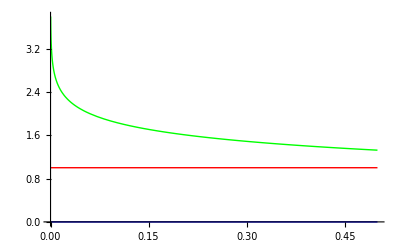

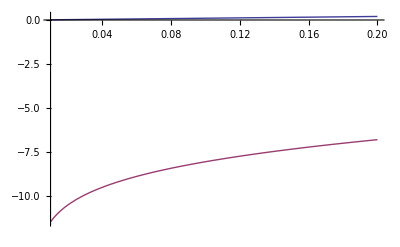

```mathematica
I0[σ_]:=-1/(4π)Log[σ/32];
Clear[s0];
λ0=4.0;
FindRoot[{1.0==λ0 I0[s0]},{s0,1}]
Plot[{1,Re[λ0 I0[s0]],Im[λ0 I0[s0]]},{s0,0.0,0.5},PlotStyle->{Red,Green,Blue}]
Plot[{s0,λ0-λ0(1+ s0/(4π)Log[s0/32])(1-λ0/(4π)(Log[s0/32]-1))},{s0,0.01,0.2}]
```

```mathematica
N[N[Log[0.059758/32]]]
```

-6.28319

I1 = 0.654289

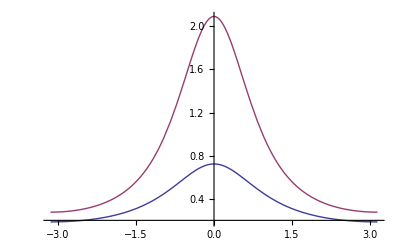

0.723147

16.7341

```mathematica
s0=1.3828453844407125;
I1=1+s0/(4π)Log[s0/32]; 
Print["I1 = ",I1];
g[k_]:=1/(4 Sin[k/2]^2+s0);
Plot[{g[k],g[k]+λ0 g[k]^2 I1},{k,-π,π},PlotRange->All]
N[1/(32 Exp[-(4π)/λ0])]
N[1/(32 Exp[-(8π)/λ0])]
```